```mathematica
(*Code created by Loïc Marrec*)
```

```mathematica
(*Description: Fixation probabilities in the island and stepping stone models - Approximation*)
```

```mathematica
(*PARAMETERS*)
```

```mathematica
bW=1; (*Wild-type birth rate*)
```

```mathematica
dW=0.1; (*Wild-type death rate*)
```

```mathematica
bM=Table[i,{i,0.95,1.1,0.001}];(*Mutant birth rate range*)
```

```mathematica
dM=0.1; (*Mutant death rate*)
```

```mathematica
Δ=5; (*Number of demes*)
```

```mathematica
Ν=100; (*Carrying capacity*)
```

```mathematica
(*SELECTION COEFFICIENTS*)
```

```mathematica
sb=bM/bW-1; (*Selection coefficient - birth*)
```

```mathematica
sd=dW/dM-1; (*Selection coefficient - death*)
```

```mathematica
s=sb+sd; (*Total selection coefficient*)
```

```mathematica
(*FIXATION PROBABILITIES*)
```

```mathematica
uM=Table[If[bM[[i]]==bW*dM/dW,1/Ν,(1-Exp[-s[[i]]])/(1-Exp[-Ν*s[[i]]])],{i,1,Length[bM]}]; (*Fixation probability of a mutant in a wild-type deme*)
```

```mathematica
(*DISPERSAL RATIOS*)
```

```mathematica
α={1/5,1/2,1,2,5}; (*Ratio of dispersal rates*)
```

```mathematica
(*GLOBAL FIXATION PROBABILITIES*)
```

```mathematica
U=Table[Module[{expr=s[[i]]+Log[α[[j]]]/Ν},If[expr==0,1/Δ,(1-Exp[-Ν*expr])/(1-Exp[-Ν*expr*Δ])]],{i,Length[s]},{j,Length[α]}];
```

```mathematica
(*DATA TABLES*)
```

```mathematica
Utable=Table[{bM[[j]]/bW-1,U[[j,i]]},{i,1,Length[α]},{j,1,Length[bM]}]; (*Single-deme fixation probability*)
```

```mathematica
utable=Table[{bM[[j]]/bW-1,uM[[j]]*U[[j,i]]},{i,1,Length[α]},{j,1,Length[bM]}]; (*Single-individual fixation probability*)
```

```mathematica
(*PLOTTING*)
```

```mathematica
colorRain=Table[ColorData["Rainbow"][k],{k,0,1,1/(Length[α]-1)}]; (*Define color scheme*)
```

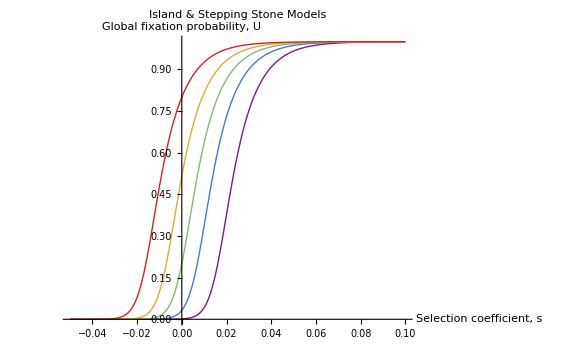

```mathematica
Show[Table[ListPlot[Utable[[f]],PlotStyle->{colorRain[[f]],Thick},Joined->True],{f,1,Length[α]}],PlotLabel->"Island & Stepping Stone Models",PlotRange->All,AxesLabel->{"Selection coefficient, s","Global fixation probability, U"},ImageSize->Large] (*Plot:Selection coefficient vs.global fixation probability*)
```